```mathematica
ClearAll["Global`*"]
```

```mathematica
D1[n_,0]:=1
D1[n_,1]:=D1[n,1]=Sum[N[Log[j]],{j,2,n}]
D1[n_, k_] := D1[n,k]=Sum[ D1[Floor[n/j],k-1],{j,2,n}]
M1[n_]:=Sum[ (-1)^(k+1) D1[n,k],{k,1,Log[2,n]}]
MM[n_,k_]:=MM[n,k]=Sum[ MoebiusMu[j] MM[Floor[n/j],k-1],{j,2,n}];MM[n_,0]:=1
mm[n_,k_]:=MM[n,k]-MM[n-1,k]
Cb[n_,k_]:=Sum[ MangoldtLambda[j] MM[Floor[n/j],k-1],{j,2,n}];Cb[n_,0]:=1
K[n_] := If[ n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
man[n_,k_]:= Log[n]-Sum[ If[ j == 1, 0, man[n/j,k+1]],{j,Divisors[n]}]
manp[n_,k_]:= Log[n]/k-Sum[ If[ j == 1, 0, manp[n/j,k+1]],{j,Divisors[n]}]
man22[n_,v_]:=If[ Floor[Log[v,n]]==Log[v,n],n Log[n] /Log[v,n],0]
manp2[n_]:=FullSimplify[manp[n,1]]-man22[n,5]
PO[n_,0]=1; 
PO[n_, k_] := PO[n,k] = Sum[ K[j]PO[Floor[n/j],k-1],{j,2,n}]
Pb[n_,k_]:=Pb[n,k]=Sum[ manp2[j] PO[Floor[n/j],k-1],{j,2,n}];Pb[n_,0]:=1
Dp[n_,z_] := Dp[n,z] = Sum[ (z^k)/(k!) Pb[n,k],{k,1, Log[2,n]}]
```

```mathematica
N[Dp[100,1]]
D1[100,1]
N[Dp[100,-1]]
M1[100]
```

98.7298

363.739

-115.046

94.0453

```mathematica
Sum[ (-1)^(k)MM[n=120,k],{k,0,Log[2,120]}]
```

120

```mathematica
D1[100,1]
N[Sum[ (-1)^(k+1)Cb[100,k],{k,1,Log[2,100]}]]
```

363.739

363.739

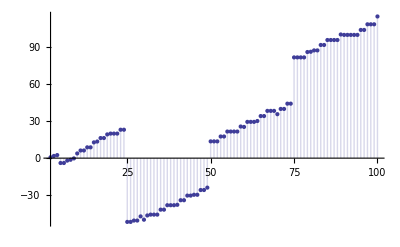

```mathematica
DiscretePlot[Dp[n,ss=-1]/ss,{n,2,100}]
```

```mathematica
Table[{n,FullSimplify[(Dp[n,ss=-1]/ss)-(Dp[n-1,ss=-1]/ss)-MangoldtLambda[n]]},{n,2,100}]//TableForm
```

2 | 0
3 | 0
4 | 0
5 | -5 Log[5]
6 | 0
7 | 0
8 | 0
9 | 0
10 | Log[25 √5]
11 | 0
12 | 0
13 | 0
14 | 0
15 | Log[25 √5]
16 | 0
17 | 0
18 | 0
19 | 0
20 | (5 Log[5])/12
21 | 0
22 | 0
23 | 0
24 | 0
25 | -(95 Log[5])/2
26 | 0
27 | 0
28 | 0
29 | 0
30 | -(5 Log[5])/3
31 | 0
32 | 0
33 | 0
34 | 0
35 | Log[25 √5]
36 | 0
37 | 0
38 | 0
39 | 0
40 | (5 Log[5])/24
41 | 0
42 | 0
43 | 0
44 | 0
45 | (5 Log[5])/12
46 | 0
47 | 0
48 | 0
49 | 0
50 | Log[11920928955078125 5^(1/3)]
51 | 0
52 | 0
53 | 0
54 | 0
55 | Log[25 √5]
56 | 0
57 | 0
58 | 0
59 | 0
60 | -(5 Log[5])/24
61 | 0
62 | 0
63 | 0
64 | 0
65 | Log[25 √5]
66 | 0
67 | 0
68 | 0
69 | 0
70 | -(5 Log[5])/3
71 | 0
72 | 0
73 | 0
74 | 0
75 | Log[11920928955078125 5^(1/3)]
76 | 0
77 | 0
78 | 0
79 | 0
80 | (19 Log[5])/144
81 | 0
82 | 0
83 | 0
84 | 0
85 | Log[25 √5]
86 | 0
87 | 0
88 | 0
89 | 0
90 | -(5 Log[5])/24
91 | 0
92 | 0
93 | 0
94 | 0
95 | Log[25 √5]
96 | 0
97 | 0
98 | 0
99 | 0
100 | Log[125 5^(23/24)]

```mathematica
vv:=2
K[n_] := If[ n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
K6[n_] := K[n]-If[ Floor[Log[vv,n]]==Log[vv,n],n /Log[vv,n],0]
P[n_,0]=1; 
P[n_, k_] := P[n,k] = Sum[ K6[j]P[Floor[n/j],k-1],{j,2,n}]
PO[n_,0]=1; 
PO[n_, k_] := PO[n,k] = Sum[ K[j]PO[Floor[n/j],k-1],{j,2,n}]
p[n_,k_]:=P[n,k]-P[n-1,k]
po[n_,k_]:=PO[n,k]-PO[n-1,k]
En[n_] := En[n] = Sum[ 1/(k!) P[n,k],{k,0, Log[2,n]}]
En[n_,z_] := En[n] = Sum[ (z^k)/(k!) P[n,k],{k,0, Log[2,n]}]
en[n_] := En[n]-En[n-1]
LAdd[n_] := Sum[ vv^k/k,{k,1,Log[vv,n]}]
LAdd2[n_] := Sum[(-1)^k vv^k,{k,1,Log[vv,n]}]
PP[n_,k_] := PP[n,k]=Sum[ 1/k-PP[Floor[n/j],k+1],{j,2,n}]
```

```mathematica
P[100,1]
```

248/15

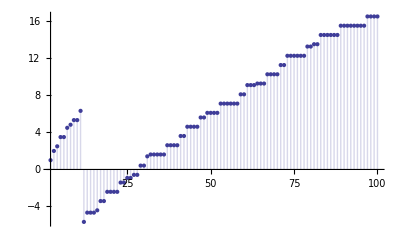

```mathematica
DiscretePlot[{P[n,1]},{n,2,100}]
```

```mathematica
Table[{n,p[n,2],po[n,2],(p[n,2]-po[n,2]),((p[n,2]-po[n,2])-If[Mod[n,vv]==0,-2(vv)po[n/vv,1],0])/(vv*vv)

},{n,9,250,9}]//TableForm
```

9 | 4 | 1 | 3 | 1
18 | -8 | 1 | -9 | -1
27 | 16 | 1 | 15 | 2
36 | -4 | 1/2 | -9/2 | -1/2
45 | -8 | 1 | -9 | -1
54 | -52/3 | 2/3 | -18 | -2
63 | -8 | 1 | -9 | -1
72 | -8/3 | 1/3 | -3 | -1/3
81 | 152/3 | 11/12 | 199/4 | 23/4
90 | 0 | 0 | 0 | 0
99 | -8 | 1 | -9 | -1
108 | -26/3 | 1/3 | -9 | -1
117 | -8 | 1 | -9 | -1
126 | 0 | 0 | 0 | 0
135 | -52/3 | 2/3 | -18 | -2
144 | -2 | 1/4 | -9/4 | -1/4
153 | -8 | 1 | -9 | -1
162 | -40 | 1/2 | -81/2 | -9/2
171 | -8 | 1 | -9 | -1
180 | 0 | 0 | 0 | 0
189 | -52/3 | 2/3 | -18 | -2
198 | 0 | 0 | 0 | 0
207 | -8 | 1 | -9 | -1
216 | -52/9 | 2/9 | -6 | -2/3
225 | -4 | 1/2 | -9/2 | -1/2
234 | 0 | 0 | 0 | 0
243 | 448/3 | 5/6 | 297/2 | 50/3

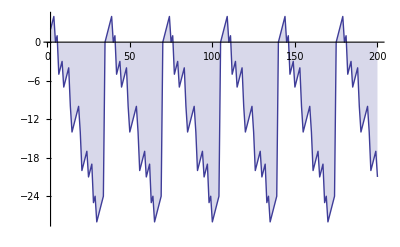

```mathematica
DiscretePlot[En[n],{n,2,200}]
```

```mathematica
Table[ {n, En[n], Mod[n,vv]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | 2 | 2
3 | 3 | 3
4 | 4 | 4
5 | 0 | 5
6 | 1 | 6
7 | -5 | 0
8 | -4 | 1
9 | -3 | 2
10 | -7 | 3
11 | -6 | 4
12 | -5 | 5
13 | -4 | 6
14 | -10 | 0
15 | -14 | 1
16 | -13 | 2
17 | -12 | 3
18 | -11 | 4
19 | -10 | 5
20 | -14 | 6
21 | -20 | 0
22 | -19 | 1
23 | -18 | 2
24 | -17 | 3
25 | -21 | 4
26 | -20 | 5
27 | -19 | 6
28 | -25 | 0
29 | -24 | 1
30 | -28 | 2
31 | -27 | 3
32 | -26 | 4
33 | -25 | 5
34 | -24 | 6
35 | 0 | 0
36 | 1 | 1
37 | 2 | 2
38 | 3 | 3
39 | 4 | 4
40 | 0 | 5
41 | 1 | 6
42 | -5 | 0
43 | -4 | 1
44 | -3 | 2
45 | -7 | 3
46 | -6 | 4
47 | -5 | 5
48 | -4 | 6
49 | -10 | 0
50 | -14 | 1
51 | -13 | 2
52 | -12 | 3
53 | -11 | 4
54 | -10 | 5
55 | -14 | 6
56 | -20 | 0
57 | -19 | 1
58 | -18 | 2
59 | -17 | 3
60 | -21 | 4
61 | -20 | 5
62 | -19 | 6
63 | -25 | 0
64 | -24 | 1
65 | -28 | 2
66 | -27 | 3
67 | -26 | 4
68 | -25 | 5
69 | -24 | 6
70 | 0 | 0
71 | 1 | 1
72 | 2 | 2
73 | 3 | 3
74 | 4 | 4
75 | 0 | 5
76 | 1 | 6
77 | -5 | 0
78 | -4 | 1
79 | -3 | 2
80 | -7 | 3
81 | -6 | 4
82 | -5 | 5
83 | -4 | 6
84 | -10 | 0
85 | -14 | 1
86 | -13 | 2
87 | -12 | 3
88 | -11 | 4
89 | -10 | 5
90 | -14 | 6
91 | -20 | 0
92 | -19 | 1
93 | -18 | 2
94 | -17 | 3
95 | -21 | 4
96 | -20 | 5
97 | -19 | 6
98 | -25 | 0
99 | -24 | 1
100 | -28 | 2

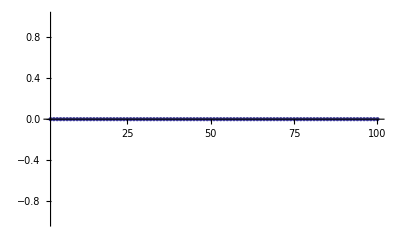

```mathematica
DiscretePlot[P[n,1]-PP[n,1]+LAdd[n]+LAdda[n],{n,2,100}]
```

```mathematica
Table[{n,P[n,2],PO[n,2],(P[n,2]-PO[n,2]),P[n,2]-PO[n,2]+2Sum[vv^j/j PO[n/vv^j,1],{j,1,Log[vv,n]}]-Sum[ vv^j vv^k/(j k),{j,1,Log[vv,n]},{k,1,Log[vv,Floor[n/(vv^j)]]}]
},{n,9,250,9}]//TableForm
```

9 | 3 | 5 | -2 | 0
18 | 47/12 | 167/12 | -10 | 0
27 | -15/4 | 283/12 | -82/3 | 0
36 | 33/4 | 383/12 | -71/3 | 0
45 | 19/12 | 463/12 | -37 | 0
54 | -115/12 | 187/4 | -169/3 | 0
63 | -53/4 | 677/12 | -209/3 | 0
72 | 653/45 | 2813/45 | -48 | 0
81 | 1067/180 | 12587/180 | -64 | 0
90 | 227/180 | 14147/180 | -232/3 | 0
99 | -365/36 | 16199/180 | -1502/15 | 0
108 | -695/36 | 16829/180 | -564/5 | 0
117 | -893/36 | 17999/180 | -624/5 | 0
126 | -929/36 | 19979/180 | -684/5 | 0
135 | 6113/180 | 4261/36 | -422/5 | 0
144 | 2479/90 | 2255/18 | -1466/15 | 0
153 | 1969/90 | 2393/18 | -1666/15 | 0
162 | 584/45 | 6383/45 | -1933/15 | 0
171 | 449/45 | 6608/45 | -2053/15 | 0
180 | 43/90 | 13801/90 | -2293/15 | 0
189 | -47/90 | 14551/90 | -811/5 | 0
198 | -1126/45 | 7403/45 | -2843/15 | 0
207 | -1096/45 | 7913/45 | -1001/5 | 0
216 | -2917/90 | 5567/30 | -9809/45 | 0
225 | -1814/45 | 2917/15 | -2113/9 | 0
234 | -2114/45 | 2957/15 | -2197/9 | 0
243 | -4153/90 | 6119/30 | -2251/9 | 0

```mathematica
Table[{n,P[n,3],
PO[n,3]
-3Sum[vv^j/j PO[n/vv^j,2],{j,1,Log[vv,n]}]
+3Sum[ vv^j vv^k/(j k) PO[n/(vv^j vv^k),1],{j,1,Log[vv,n]},{k,1,Log[vv,Floor[n/(vv^j)]]}]
-Sum[ vv^j vv^k vv^m/(j k m) PO[n/(vv^j vv^k vv^m),0],{j,1,Log[vv,n]},{k,1,Log[vv,Floor[n/(vv^j)]]},{m,1,Log[vv,Floor[n/(vv^j vv^k)]]}]
},{n,9,250,9}]//TableForm
```

9 | -1 | -1
18 | -11/2 | -11/2
27 | 15/2 | 15/2
36 | -49/4 | -49/4
45 | -13/4 | -13/4
54 | 29/2 | 29/2
63 | 35/2 | 35/2
72 | -237/8 | -237/8
81 | -59/8 | -59/8
90 | -83/8 | -83/8
99 | 289/8 | 289/8
108 | 309/8 | 309/8
117 | 427/8 | 427/8
126 | 323/8 | 323/8
135 | -6727/120 | -6727/120
144 | -944/15 | -944/15
153 | -719/15 | -719/15
162 | -1331/60 | -1331/60
171 | -1811/60 | -1811/60
180 | -209/15 | -209/15
189 | -164/15 | -164/15
198 | 1407/20 | 1407/20
207 | 1237/20 | 1237/20
216 | 408/5 | 408/5
225 | 1131/10 | 1131/10
234 | 1101/10 | 1101/10
243 | 1667/20 | 1667/20

```mathematica
Table[{n,P[n,3],
PO[n,3]
-3Sum[vv^j/j PO[n/vv^j,2],{j,1,Log[vv,n]}]
+3Sum[ vv^(j+k)/(j k) PO[n/(vv^(j+k)),1],{j,1,Log[vv,n]},{k,1,Log[vv,Floor[n/(vv^j)]]}]
-Sum[ vv^(j+k+m)/(j k m) PO[n/(vv^(j+k+m)),0],{j,1,Log[vv,n]},{k,1,Log[vv,Floor[n/(vv^j)]]},{m,1,Log[vv,Floor[n/(vv^(j+k))]]}]
},{n,2,50,1}]//TableForm
```

2 | 0 | 0
3 | 0 | 0
4 | 0 | 0
5 | 0 | 0
6 | 0 | 0
7 | 0 | 0
8 | -1 | -1
9 | -1 | -1
10 | -1 | -1
11 | -1 | -1
12 | 2 | 2
13 | 2 | 2
14 | 2 | 2
15 | 2 | 2
16 | -5/2 | -5/2
17 | -5/2 | -5/2
18 | -11/2 | -11/2
19 | -11/2 | -11/2
20 | -5/2 | -5/2
21 | -5/2 | -5/2
22 | -5/2 | -5/2
23 | -5/2 | -5/2
24 | 13/2 | 13/2
25 | 13/2 | 13/2
26 | 13/2 | 13/2
27 | 15/2 | 15/2
28 | 21/2 | 21/2
29 | 21/2 | 21/2
30 | 9/2 | 9/2
31 | 9/2 | 9/2
32 | -37/4 | -37/4
33 | -37/4 | -37/4
34 | -37/4 | -37/4
35 | -37/4 | -37/4
36 | -49/4 | -49/4
37 | -49/4 | -49/4
38 | -49/4 | -49/4
39 | -49/4 | -49/4
40 | -13/4 | -13/4
41 | -13/4 | -13/4
42 | -37/4 | -37/4
43 | -37/4 | -37/4
44 | -25/4 | -25/4
45 | -13/4 | -13/4
46 | -13/4 | -13/4
47 | -13/4 | -13/4
48 | 35/2 | 35/2
49 | 35/2 | 35/2
50 | 29/2 | 29/2

```mathematica
fd[n_]:=Sum[ vv^(j+k)/(j k ),{j,1,Log[vv,n]},{k,1,Log[vv,Floor[n/(vv^j)]]}]
fe[n_]:=Sum[ vv^(j+k+m)/(j k m) ,{j,1,Log[vv,n]},{k,1,Log[vv,Floor[n/(vv^j)]]},{m,1,Log[vv,Floor[n/(vv^(j+k))]]}]
```

```mathematica
Table[{n,(fe[n]-fe[n-1])/n},{n,8,800,8}]//TableForm
```

8 | 1
16 | 3/2
24 | 0
32 | 7/4
40 | 0
48 | 0
56 | 0
64 | 15/8
72 | 0
80 | 0
88 | 0
96 | 0
104 | 0
112 | 0
120 | 0
128 | 29/15
136 | 0
144 | 0
152 | 0
160 | 0
168 | 0
176 | 0
184 | 0
192 | 0
200 | 0
208 | 0
216 | 0
224 | 0
232 | 0
240 | 0
248 | 0
256 | 469/240
264 | 0
272 | 0
280 | 0
288 | 0
296 | 0
304 | 0
312 | 0
320 | 0
328 | 0
336 | 0
344 | 0
352 | 0
360 | 0
368 | 0
376 | 0
384 | 0
392 | 0
400 | 0
408 | 0
416 | 0
424 | 0
432 | 0
440 | 0
448 | 0
456 | 0
464 | 0
472 | 0
480 | 0
488 | 0
496 | 0
504 | 0
512 | 29531/15120
520 | 0
528 | 0
536 | 0
544 | 0
552 | 0
560 | 0
568 | 0
576 | 0
584 | 0
592 | 0
600 | 0
608 | 0
616 | 0
624 | 0
632 | 0
640 | 0
648 | 0
656 | 0
664 | 0
672 | 0
680 | 0
688 | 0
696 | 0
704 | 0
712 | 0
720 | 0
728 | 0
736 | 0
744 | 0
752 | 0
760 | 0
768 | 0
776 | 0
784 | 0
792 | 0
800 | 0

```mathematica
ff[s_]:=f[5]/5^s
```

```mathematica
ff'[s]
```

-5^-s f[5] Log[5]